# Parser

Parser for the grammar:

## Recursive descent parser

```mathematica
MapUntilArg[f_,expr_,test_]:=Drop[
NestWhileList[
{f[#[[2,1]]],Drop[#[[2]],1],(!test[#[[2,1]]] && Length[#[[2]]]≠1)}&,
{0,expr,True},
#[[3]]&
][[All,1]],
1];

MapUntil[f_,expr_,test_]:=Drop[
NestWhileList[
{f[#[[2,1]]],Drop[#[[2]],1],(!test[f[#[[2,1]]]]&& Length[#[[2]]]≠1)}&,
{0,expr,True},
#[[3]]&
][[All,1]],
1];

MapWhileArg[f_,expr_,test_]:=Drop[
NestWhileList[
{f[#[[2,1]]],Drop[#[[2]],1]}&,
{0,expr},
test[#[[2,1]]]&
][[All,1]],
1];
```

```mathematica
MapUntil[f,Range[5],#=!=$Failed&]
```

{$Failed,2}

```mathematica
MapUntil[f,Range[5],#===7&]
```

{$Failed,2,3,4,5}

```mathematica
Protect[EmptyString,Term,NonTerm];

Match[input_,terms_]:=(Take[input,Length[terms]] == terms);
GetArgument[_[arg_]]:=arg;

MatchTerminalsWithRule[input_,rule_]:=Block[{terms,rest,matched,cuttedInput,currentState = rule["From"]},
If[rule["To"]===EmptyString,Return[{{currentState->EmptyString},{},input}]];

terms = MapWhileArg[GetArgument,rule["To"],Head[#]=!=NonTerm&];
rest = Drop[rule["To"],Length[terms]];

If[Length[terms]>Length[input],Return[$Failed]];

If[Match[input,terms],
matched = Thread[currentState->terms];
cuttedInput = Drop[input,Length[terms]];
Return[{matched,rest,cuttedInput}];
,
Return[$Failed];
];
];

MatchTerminals[state_,input_,grammar_]:=Block[{possibleTransitions,matched},
possibleTransitions = Cases[grammar,KeyValuePattern[{"From"->state}]];
matched = Last[MapUntil[MatchTerminalsWithRule[input,#]&,possibleTransitions,#=!=$Failed&]];
Return[matched];
];
```

```mathematica
grammar = {
<|"From"->NonTerm["E"],"To"->{Term["i"],NonTerm["E'"],NonTerm["V"]}|>,
<|"From"->NonTerm["V"],"To"->{Term["j"],NonTerm["V"]}|>,
<|"From"->NonTerm["V"],"To"->EmptyString|>,
<|"From"->NonTerm["E'"],"To"->{Term["+"],Term["i"],NonTerm["E'"]}|>,
<|"From"->NonTerm["E'"],"To"->EmptyString|>
};
```

```mathematica
MatchTerminals["E'",{"+","i","$"},grammar]
```

{{E'→+,E'→i},{NonTerm[E']},{$}}

Parse

```mathematica
AddIdToSingleTransition[n_,m_,a_->b_]:={n,a}->{m,b};
AddIdToTransition[currentId_,transitions_]:=MapIndexed[AddIdToSingleTransition[currentId,currentId+First[#2],#1]&,transitions];
StackSymbols[caller_,id_,list_]:=Map[<|"Caller"->caller,"Id"->id,"Symbol"->#|>&,list];

Parse[input_,grammar_]:=Block[{start,inputBuffer,enter,parseTree,stack,transitions,next,currentId,newId},
start = First[grammar]["From"];
inputBuffer = Characters[StringJoin[input,"$"]];

enter = start;
parseTree = {};
stack ={};
currentId = 0;

While[{inputBuffer,enter} =!= {{"$"},None},

{transitions,next,inputBuffer}=MatchTerminals[enter,inputBuffer,grammar];

AppendTo[parseTree,AddIdToTransition[currentId,transitions]];
newId = currentId+Length[transitions];

If[Length[next] > 0,
AppendTo[parseTree,{currentId,enter}->{newId+1,First[next]}];
{enter,stack} ={First[next],Join[stack,StackSymbols[enter,newId,Rest[next]]]};
,
If[Length[stack] > 0,
AppendTo[parseTree,{Last[stack]["Id"],Last[stack]["Caller"]}->{newId+1,Last[stack]["Symbol"]}];
{enter,stack} = {Last[stack]["Symbol"],Drop[stack,-1]};
,
enter = None;
]
];

currentId= newId+1;
];

Return[Flatten[parseTree,1]];

];

ParseTree[input_,grammar_]:=Block[{parseTree,startProduction},
parseTree = Parse[input,grammar];
startProduction = First[First[parseTree]];

TreePlot[parseTree,Automatic,startProduction,VertexLabeling->True]
];
```

```mathematica
Parse["i+i+ijj",grammar]
```

{{0,NonTerm[E]}→{1,i},{0,NonTerm[E]}→{2,NonTerm[E']},{2,NonTerm[E']}→{3,+},{2,NonTerm[E']}→{4,i},{2,NonTerm[E']}→{5,NonTerm[E']},{5,NonTerm[E']}→{6,+},{5,NonTerm[E']}→{7,i},{5,NonTerm[E']}→{8,NonTerm[E']},{8,NonTerm[E']}→{9,EmptyString},{1,NonTerm[E]}→{10,NonTerm[V]},{10,NonTerm[V]}→{11,j},{10,NonTerm[V]}→{12,NonTerm[V]},{12,NonTerm[V]}→{13,j},{12,NonTerm[V]}→{14,NonTerm[V]},{14,NonTerm[V]}→{15,EmptyString}}

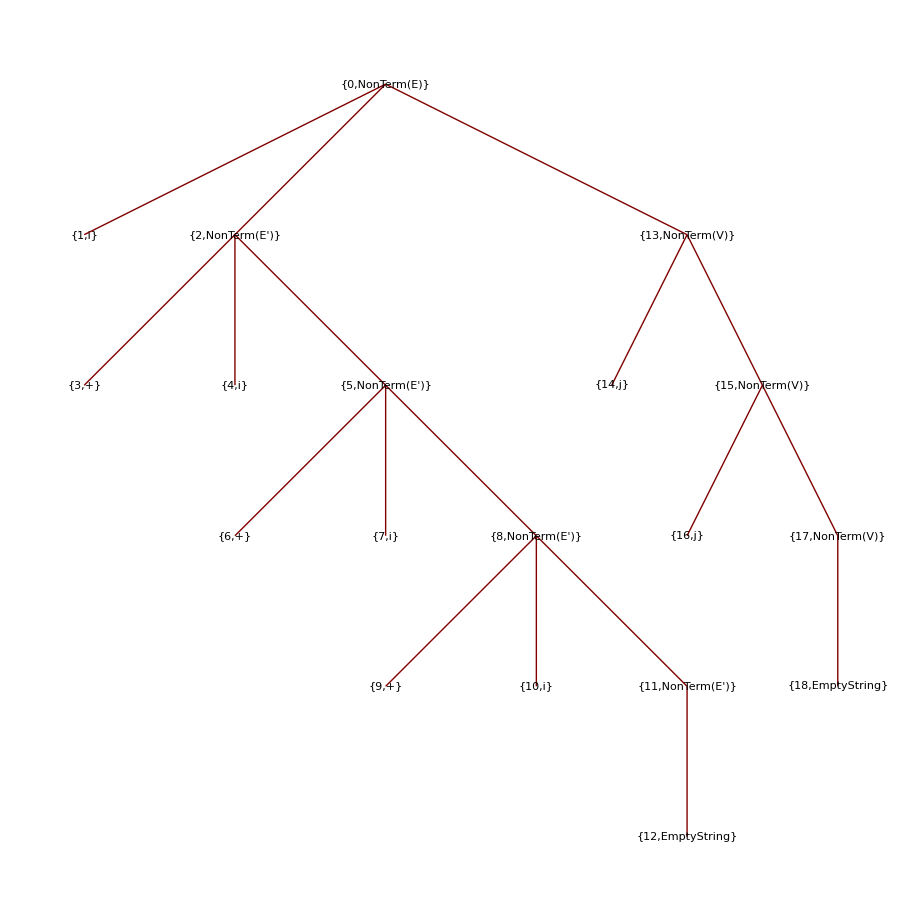

```mathematica
ParseTree["i+i+i+ijj",grammar]
```

```mathematica
.b4
```